```mathematica
SetDirectory["N:\\0MPX\\num300\\num300B"];   
<<param\\paramCertain; (* certain param *)
<<param\\paramUncert;    (* matrix with sets of values for uncert param *)
<<param\\NSympALLinitialParam;
```

```mathematica
Tmax=91;            (* #days to run *)
ndataFit=73;
nsim=nmaxsim;  (* #param sets *)  (*  nmaxsimB=nmaxsim;*)
tpoint=Table[it,{it,0,Tmax,1}];ntpoints=Length[tpoint];

upSelBMat  =Array[upSelB,{nsim,Kpar}];
xSelBMat    =Array[xSelB,  {nsim}];
rSelBMat    =Array[rSelB,  {nsim}];

(*----------- IMPORT DATA TO FIT  -------------------*)
dataAll=Flatten[Import["CasesPerOnsetDate.xls"]];
tofit     =dataAll(*Flatten[Import["onset20220427to20220829weekaverage.xls"]]*);
dataFit=Table[tofit[[j]],{j,1,ndataFit}];(* use onset dates 27042022 up to & including 25072022 *)
```

```mathematica
(*----------------select 1: FIT TO DATA T=20-90 *)
pl=Table[Product[nSymp[k][[j]]^dataFit[[k]]*Exp[-nSymp[k][[j]]]/Factorial[dataFit[[k]]],{k,2,ndataFit}], {j,1,nsim}] ;(* Poisson Likelihood *) 
cw=Table[Sum[pl[[js]],{js,1,j}], {j,1,nsim}]/Sum[pl[[jk]],{jk,1,nsim}];(* cumulative weights: w1, w1+w2, ..., w1+w2+...+wNSIM *)
U=RandomReal[1,nsim]; (* sample nsim values from U(0,1) distribution *) 

(* Count how many of the U(0,1) values sampled are in each interval (CumW[k],CumW[k+1])  *)
cc[1]=Count[U,u_/;u<=cw[[1]]];
Do[cc[k]=Count[U,u_/;cw[[k-1]]<u<=cw[[k]]]
,{k,2,nsim}];

nSelB=0;  
Do[     
If[cc[j]>0 ,
(*THEN*) nSelB=nSelB+1;xSelB[j]=1;rSelB[nSelB]=cc[j];Do[upSelB[nSelB,ipar]=upAll[j,ipar],{ipar,1,Kpar}]  ,
(*ELSE*) xSelB[j]=0], (* close If *)
{j,nsim}]; (* close Do *)
s1=Select[Range[nsim],xSelB[#]==0&];
s2=Select[Range[nsim],xSelB[#]== 1&];
indexSelB=s2;
Print["Number of par sets selected = ", nSelB]
nmaxsimB=Sum[rSelB[j],{j,nSelB}]
```

Number of par sets selected = 216

10000

```mathematica
(* COMBINE FILES OF SEPARATE SELECTIONS *)
nSel=nSelB;  
nsim=nSel;
nmaxsim=nmaxsimB;
upSelMat  =Array[upSel,{nsim,Kpar}];

Do[     
rSel[j]=rSelB[j];
Do[upSel[j,k]=upSelB[j,k],{k,1,Kpar}];
,{j,nSelB}];

Print["nSelB,nSelC,nSelD,nSel = ",{nSelB,nSelC,nSelD,nSel}]
Print["nmaxsimB,nmaxsimC,nmaxsimD,nmaxsim = ",{nmaxsimB,nmaxsimC,nmaxsimD,nmaxsim}]
Print["Sum[rSelB],Sum[rSelC],Sum[rSelD],Sum[rSel] = ",{Sum[rSelB[j],{j,nSelB}],Sum[rSelC[j],{j,nSelC}],Sum[rSelD[j],{j,nSelD}],Sum[rSel[j],{j,nSel}]}]
```

nSelB,nSelC,nSelD,nSel = {216,nSelC,nSelD,216}

nmaxsimB,nmaxsimC,nmaxsimD,nmaxsim = {10000,nmaxsimC,nmaxsimD,10000}

Sum[rSelB],Sum[rSelC],Sum[rSelD],Sum[rSel] = {10000,∑_j^nSelC rSelC[j],∑_j^nSelD rSelD[j],10000}

```mathematica
(*********************************************************************)
Save["param\\paramUncertSelected73BCD",  {rSel,nSel,nmaxsim,upSelMat,Tmax,dataFit,ndataFit,dataAll}]
(*********************************************************************)
```

```mathematica
Do[t=tpoint[[it]];
nSympAll[it]=Flatten[Table[Table[nSymp[it][[s2[[j]]]],rSelB[j]] ,{j,nSelB}]];
cumSympAll[it]=Sum[nSympAll[kk],{kk,1,it}];
,{it,1,ntpoints}]
```

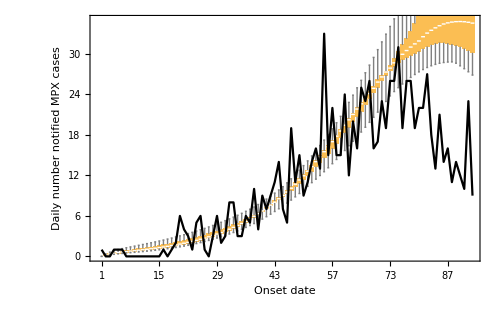

```mathematica
Show[ 
BoxWhiskerChart[Table[Table[nSympAll[it][[j]], {j,nmaxsimB}],{it,Tmax}],PlotRange->{{0,Tmax},{0,35}},BaseStyle->{FontFamily->"Arial",FontSize->12},
ChartLabels->{"1","","","","","","","8","","","","","","","15","","","","","","","22","","","","","","","29","","","","","","","36","","","","","","","43","","","","","","","50","","","","","","","57","","","","","","","64","","","","","","","73","","","","","","","80","","","","","","","87","","","","","","","94","","","","","","","101","","","","","","","108","","","","","","","115"},Frame->{True,True,False,False},FrameLabel->{"Onset date","Daily number notified MPX cases"}],
ListPlot[Table[{it,dataAll[[it]]},{it,1,Tmax}],PlotStyle->{Black},Joined->True],
ImageSize->500]
```